# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

AppendTo[$Path,"/Users/thomasbuhrmann/Library/Mathematica/Packages/LevelScheme"];
Get["LevelScheme`"];

(* Best *)
dirNameB1 = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_01_16__12_26_42"; (* Mv1234 0.994 *)
dirNameB2 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_04__17_49_45"; (* Mv1234 0.992 *)
dirNameB3 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_30__13_57_40"; (* Mv24 0.9918 *)
dirNameB4 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_27__21_30_56"; (* Mv1234 0.9928 *)
dirNameB5 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_19__21_52_30"; (* Mv1234 0.9918 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_03_21__13_38_43"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_11__17_43_03"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_25__14_55_44"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_26__15_44_55"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_27__00_48_28"; (* *)

(* Ablation *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__14_01_20"; (* Like above, but without IbInterseg: 0.984 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__19_52_19"; (* Like above, but without IbIaExc: 0.975 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_23__10_26_30"; (* Like above, but no Ib at all: 0.970 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55"; (* No interneurons at all, but GO sig *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_09__20_37_11"; (* Mv123456 Run from _19_47_32 *)

(* Dirs 8M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_13__16_02_25"; (* 8M: 0.946. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__02_07_37"; (* 8M: 0.95. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_19__20_45_29/"; (* 0.961 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_21__11_58_38/"; (* 0.965 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_08_20__16_48_48"; (* 8M_2: 0.952. Not good. *)

(* Dirs 6M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__19_15_19"; (* 6M_1: 0.967. Two moves bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_16__10_04_00"; (* 6M_1 inc: 0.9723. Still two bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_17__14_13_56"; (* 6M_1 inc2: 0.987. Pretty good. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__11_25_57/"; (* 6M_2: 0.967. Two moves bad again. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__13_22_34/"; (* 6M_2: 0.9685. Two moves bad again. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_54_14/"; (*!! 6M_3: 0.989.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_57_09/"; (* 6M_3: 0.9889.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_02"; (* 6M_3: 0.979.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_11"; (* 6M_3: 0.976.*)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__10_31_25/"; (* 6M_3: 0.983. Weird hook. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__00_06_01/"; (* 6M_3: 0.9825. Weird hook*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_57_34/"; (*!! 6M_3: 0.98.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_49_02/"; (* 6M_3: 0.9785.*)

(* Dirs 4M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_31"; (*!! 4M diag: 0.9916 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_29"; (*!! 4M diag: 0.9914 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Dirs/0/13_07_08__16_18_21/"; (* 4M straight, slow: 0.991. Wobbly. *)
(* Mv1234 check whether 4M net works for 1234: 0.96011, 0.946. No! *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10/"; 

(* Energy min *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_18__18_39_18/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__09_46_01/"; (* network: 1.98171 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__10_56_15/"; (* network asymsp: 1.98431 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__11_40_37/";(* network symsp noVelRef: 1.98415 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__14_11_55/";(* R1 network symsp noVelRef: 1.9839 *)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__10_06_33/"; (* Engy min PD: 1.982 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_26_06/"; (* Engy min PD noVelRef: 0.993 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_33_04/"; (* Engy min PD noVelRef dbgain: 0.9934 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_46_28/"; (* Engy min PD noVelRef higher gain: 0.994 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_52_51/"; 
(* Engy min PD noVelRef higher gain, exp:  *)

(* PD control multiple movements *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_20__15_56_46/"; (* 6M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__20_53_06"; (* 4M PD min engy: *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_02_06__22_44_11";*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_21__15_16_27"; (* Mv1234 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_17__17_18_17"; (* Mv1234 *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_19__19_38_08"; (* Mv34 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_18__14_18_53"; (* Mv12 Ext OL *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_17__15_14_34"; (* Mv12 Norm OL *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_16__17_44_26"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_06_10__02_25_24"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_12__19_20_02/"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; (* Mv1 *)*)

figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";
SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.53 (January 10, 2013)
View color paletteVisit home page  -Graphics-

2400

## Fitness

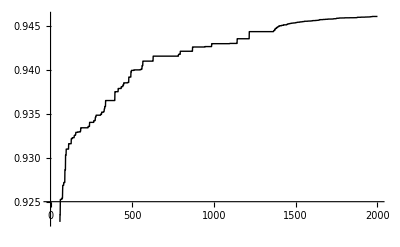

0.946034

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->Automatic,ImageSize->400]
maxFit = Max[fitness]
```

## Robustness

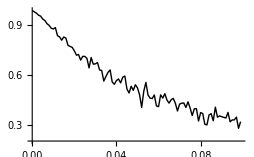

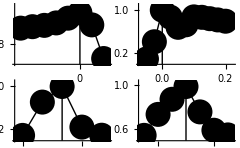

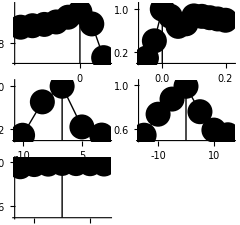

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/generalisation.eps

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/readaptConstVel.eps

```mathematica
(* Mutations *)
SetDirectory["/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__19_27_46"];
mutFitData=Import["Fitness.txt", "Table"];
fitData = mutFitData[[2;;-2]];
mutFit =fitData[[;;,1]];
grouped = Partition[mutFit,100];
means=Mean[Transpose[grouped]];
Length[means];
x=Range[0,0.099,0.001];
Length[x];
cm=72/2.54;
robPl=ListLinePlot[Transpose[{x,means}],PlotStyle->Black,AxesOrigin->{0,0.2},ImageSize->9cm]
(*Export[figExpPath<>"robustness.svg",robPl]*)

(* Shifts *)
(*opts={PlotMarkers->None,PlotStyle->Black,FillingStyle->{Black,AbsoluteThickness[10]},Filling->Axis,BaseStyle->{FontFamily->font}};*)
opts={PlotStyle->Black,BaseStyle->{FontFamily->font},Mesh->All,MeshStyle->{PointSize[0.045],Black},BaseStyle->{FontFamily->font}};
SetOptions[LinTicks,MajorTickLength->{0.03,0},MinorTickLength->{0.01,0},ShowMinorTicks->False];

shiftFit={0.896, 0.905,0.913,0.928,0.957,0.9896,0.916,0.71};
x=Range[-25,10,5];
shiftPl=ListLinePlot[Transpose[{x,shiftFit}],AxesOrigin->{-27.5,0.95*Min[shiftFit]},PlotRange->{{-27.5,12.5},{0.95*Min[shiftFit],1.05*Max[shiftFit]}},opts,
Ticks->{LinTicks[-30,10],LinTicks[0.5,1]}, 
Epilog->{Line[{{0,0.95*Min[shiftFit]},{0,Max[shiftFit]}}]}];
shiftPl = Show[shiftPl];

(* Durations *)
durFits = {0.088,0.406,0.9896,0.8607,0.6723,0.719,0.865,0.857,0.832,0.809,0.785};
x=Range[-0.05,0.2,0.025];
durPl=ListLinePlot[Transpose[{x,durFits}],AxesOrigin->{-0.075,Min[durFits]-0.1*Max[durFits]},PlotRange->{{-0.075,0.225},{Min[durFits]-0.1*Max[durFits],1.1*Max[durFits]}},opts,
Ticks->{LinTicks[-0.05,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[durFits]-0.1*Max[durFits]},{0,Max[durFits]}}]}];

(* Amplitudes *)
ampFits = {0.0818,0.7,0.9896,0.2356,0.085};
x=Range[-10,10,5];
ampPl=ListLinePlot[Transpose[{x,ampFits}],AxesOrigin->{-12,Min[ampFits]-0.1*Max[ampFits]},PlotRange->{{-12,12},{Min[ampFits]-0.1*Max[ampFits],1.1*Max[ampFits]}},opts,
Ticks->{LinTicks[-10,10],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[ampFits]-0.1*Max[ampFits]},{0,Max[ampFits]}}]}];

(* Const velocity (changing duration and amplitude in proportion) *)
velFits = {0.54, 0.733,0.872,0.9896,0.756,0.587,0.544};
x=Range[-15,15,5];
velPl=ListLinePlot[Transpose[{x,velFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,
Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[velFits]-0.05*Max[velFits]},{0,Max[velFits]}}]}];

(* Readapted Const velocity (changing duration and amplitude in proportion) *)
revelFits = {0.959, 0.979,0.983,0.9896,0.988,0.987,0.984};
x=Range[-15,15,5];
revelPl=ListLinePlot[Transpose[{x,revelFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]},
Epilog->{Line[{{0,Min[velFits]-0.05*Max[revelFits]},{0,Max[revelFits]}}]} ];

general=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl}}], ImageSize->8.5cm]
readapt=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl},{revelPl}}], ImageSize->8.5cm]
(*readapt = Show[revelPl, ImageSize->8.5cm]*)

Export[figExpPath<>"generalisation.eps",general]
Export[figExpPath<>"readaptConstVel.eps",readapt]

SetDirectory[dirName];
```

## Config

```mathematica
dt = 0.001;
leadIn = 0.1;
leadOut = 0.2;
moveDuration = 0.3;
bestFitDelay = -0.0 / dt;
(*plotDuration = (moveDuration+leadOut/3) / dt;*)

trialDuration = leadIn+moveDuration+leadOut;
frontLead =0.1;
backLead = 1.0*leadOut;

numTrials=Round[numData/(trialDuration/dt)]

SetTrial[trial_]:=Module[{},
t0=2 +((leadIn-frontLead+ (trial*trialDuration))/dt);
tn=-2 +t0+(leadIn + moveDuration+backLead)/dt;
time=Range[tn-t0]*dt;
];

SetTrial[0];

padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
font="Arial";
SetOptions[Plot,BaseStyle->{FontFamily->font}];
pad={{20,10},{15,10}};
```

4.

4

4

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, delay_:0]:=Table[data[[i,NtoI[name]]],{i,t0+delay,tn-1+delay}];
TimePlot[name_, options_, delay_:0,Scale_:1] := ListLinePlot[Transpose[{time,Scale*NtoD[name, delay]}], Join[options,plotOptions]];
TimePlotD[data_, options_, Scale_:1] := ListLinePlot[Transpose[{time,Scale*data}], Join[plotOptions,options]];

Maxima[x_,time_]:=Module[{max,peaks, times},
max = 1+Position[Differences[Sign[Differences[x]]],-2];
peaks = Extract[x, max];
times = Extract[time,max];
maxima = Transpose[{Flatten[times],peaks}];
maxima
]

Minima[x_,time_]:=Module[{min,peaks, times},
min = 1+Position[Differences[Sign[Differences[-x]]],-2];
peaks = -Extract[-x, min];
times = Extract[time,min];
minima = Transpose[{Flatten[times],peaks}];
minima
]

TimePlotMaxima[x_,time_, opt_:{}]:= ListPlot[Maxima[x,time],opt]
TimePlotMinima[x_,time_,opt_:{}]:= ListPlot[Minima[x,time],opt]
TimePlotOptima[x_, time_, opt1_:{},opt2_:{}]:=Module[{ma,mi},
ma=TimePlotMaxima[x, time,Join[{PlotStyle->Black},opt1]];
mi=TimePlotMinima[x,time,Join[{PlotStyle->Red},opt2]];
mami=Show[ma, mi];
mami
]

Shift[list_,del_]:=Module[{},
res=Drop[list,del];
res = If[del<0,
PadLeft[res,Length[list],res[[1]]],
PadRight[res,Length[list],res[[Length[res]]]]
]
];

(*l=Range[0,10]
l4=Shift[l,-2]*)
```

## All trajectories

28.3465

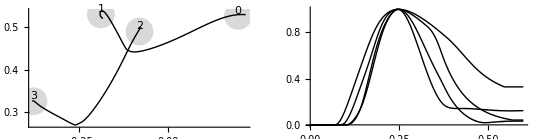

```mathematica
PlotTraj[trial_]:=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
elbX=NtoD["elbX"];
elbY=NtoD["elbY"];
desX=NtoD["desX"];
desY=NtoD["desY"];
positions=Transpose[{x,y}];
elbPositions=Transpose[{elbX,elbY}];
desPositions=Transpose[{desX,desY}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->{Black},AxesOrigin->{Min[x],Min[y]}];
pos0=First[positions];
elb0=First[elbPositions];
posN=Last[positions];
elbN=Last[elbPositions];
startPos = Graphics[{PointSize[Large],Point[pos0]}];
elbStartPos = Graphics[{LightGray,PointSize[Large],Point[elb0]}];
desEndPos=Graphics[{LightGray,PointSize[0.05],Point[Last[desPositions]]}];
label=Graphics[Text[trial,Last[desPositions],{0,-2}]];
lower0=Graphics[{LightGray,Line[{elb0, pos0}]}];
upper0=Graphics[{LightGray,Line[{{0,0}, elb0}]}];
lowerN=Graphics[{LightGray,Line[{elbN, posN}]}];
upperN=Graphics[{LightGray,Line[{{0,0}, elbN}]}];
optimal = Graphics[{LightGray,Dashed,Line[{pos0, Last[desPositions]}]}];
Show[(*elbStartPos,lower0,upper0,*)(*lowerN,upperN, optimal,*) (*startPos,*)desEndPos,cartesianPos,label,BaseStyle->{FontFamily->font}]
]

TangVels[trial_] :=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]]
]

MaxTangVelPos[trial_]:=Module[{}, tangVels = TangVels[trial];Position[tangVels,Max[tangVels]][[1]] ]
maxVelPos = Flatten[Map[MaxTangVelPos,Range[0,numTrials-1,1]]];
velOff = maxVelPos-Min[maxVelPos];

PlotTangVels[trial_]:=Module[{},
vels=TangVels[trial];
(* Shift so peaks coincide *)
vels = Drop[vels,velOff[[trial+1]]];
vels=PadRight[vels,Length[vels]+velOff[[trial+1]], Last[vels]];
(* Scale to same peak *)
maxVel =Max[Map[Norm,vels]];
vels = vels / maxVel;
col = Black;(*If[trial < 2,Black,Gray];*)
ln = {};(*If[EvenQ[trial],{},Dashed];*)
tangVel=TimePlotD[vels,{PlotStyle->{col, ln},BaseStyle->{FontFamily->font}}]
];

PlotAngles[trial_,mmin_:50,mmax_:100]:=Module[{},
SetTrial[trial];
shdAng=NtoD["angleShoulder"]/Degree;
shdAngDes=NtoD["desShoulder"]/Degree;
shdAngCom =NtoD["comShoulder"]/Degree;
elbAng=NtoD["angleElbow"]/Degree;
elbAngDes=NtoD["desElbow"]/Degree;
elbAngCom =NtoD["comElbow"]/Degree;
min=Min[Min[elbAng],Min[shdAng]]*0.9;
max=Max[Max[elbAng],Max[shdAng]]*1.1;
shdPl= TimePlotD[shdAng,{PlotStyle->{Black}}];
shdPlDes= TimePlotD[shdAngDes,{PlotStyle->{LightGray,Thick}}];
shdPlCom= TimePlotD[shdAngCom,{PlotStyle->{Black,Dashed}}];
elbPl= TimePlotD[elbAng,{PlotStyle->{Black}}];
elbPlDes= TimePlotD[elbAngDes,{PlotStyle->{LightGray,Thick}}];
elbPlCom= TimePlotD[elbAngCom,{PlotStyle->{Black,Dashed}}];
Show[elbPlDes, shdPlDes,shdPl,elbPl,shdPlCom,elbPlCom,PlotRange->{{0,0.6},{min,max}},AxesOrigin->{0,min},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[mmin,mmax,TickLabelStep->2,TickLabelStart->1]} ]
];

PlotAngVels[trial_]:=Module[{},
SetTrial[trial];
shdVel=NtoD["velocityShoulder"]/Degree;
elbVel=NtoD["velocityElbow"]/Degree;
shdPl= TimePlotD[shdVel,{PlotStyle->{Black}}];
elbPl= TimePlotD[elbVel,{PlotStyle->{Black,Dashed}}];
Show[elbPl, shdPl]
];

(* Forces applied at joints, total is more or less acceleration *)
PlotTrqsElb[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msD = NtoD["torqueElbow"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}}];
trq= TimePlotD[msD,{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin = 1.1*Min[{Min[itD],Min[msD],Min[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,Automatic}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0]} ]
]

PlotAMNElb[trial_]:=Module[{},
SetTrial[trial];
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ]
]

PlotAMNShd[trial_]:=Module[{},
SetTrial[trial];
aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ]
]

PlotTrqMElb[trial_]:=Module[{},
SetTrial[trial];
elbAgTrq = NtoD["ElbowFlexorTorque"];
elbAnTrq = NtoD["ElbowExtensorTorque"];
elbNetTrq = elbAgTrq - elbAnTrq;
max = Max[Max[Abs[elbAgTrq]],Max[Abs[elbAnTrq]],Max[Abs[elbNetTrq]]];
elbAgTorqueP = TimePlotD[elbAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbAnTorqueP = TimePlotD[elbAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
elbNetTrqP = TimePlotD[elbNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbTrq = Show[elbNetTrqP,elbAgTorqueP,elbAnTorqueP, PlotRange->{Automatic,{-max, max}}]
]

PlotTrqMShd[trial_]:=Module[{},
SetTrial[trial];
shdAgTrq = NtoD["ShoulderFlexorTorque"];
shdAnTrq = NtoD["ShoulderExtensorTorque"];
shdNetTrq = shdAgTrq - shdAnTrq;
max = Max[Max[Abs[shdAgTrq]],Max[Abs[shdAnTrq]],Max[Abs[shdNetTrq]]];
shdAgTorqueP = TimePlotD[shdAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}},ImageSize->2cm}];
shdAnTorqueP = TimePlotD[shdAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
shdNetTrqP = TimePlotD[shdNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
shdTrq = Show[shdNetTrqP,shdAgTorqueP,shdAnTorqueP,PlotRange->{Automatic,{-max, max}}]
]

PlotTrqsShd[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
msD = NtoD["torqueShoulder"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},ImageSize->22cm}];
trq= TimePlot["torqueShoulder",{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin =1.1* Min[{Min[itD],Min[msD],Min[totalD]}];
mmax =1.1* Max[{Max[itD],Max[msD],Max[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,mmax}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0,ShowMinorTicks->False]}]
]

trajsPl = Show[Table[PlotTraj[i],{i,0,numTrials-1}], Axes->True,AxesOrigin->{-0.45,0.25},ImagePadding->pad,AxesStyle->Thickness[.002]];


tangVelsPl=Show[Table[PlotTangVels[i],{i,0,numTrials-1}](*AspectRatio->1,*), ImagePadding->pad,AxesStyle->Thickness[.002]];

cm=72/2.54
angAndVel=Show[GraphicsRow[{trajsPl, tangVelsPl}],ImageSize->19cm]

(*Export[figExpPath<>"TrajStar4M2.eps",trajsPl]*)
(*Export[figExpPath<>"c1TrajAndVelNoIbIs.eps",angAndVel]*)

(*GraphicsGrid[Partition[Table[PlotAngles[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotAngVels[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotTrqsElb[i],{i,0,numTrials-1}],2],ImageSize->600]*)
tr1=0;
tr2=1;

(*mv12=GraphicsGrid[{{PlotAngles[tr1,40,90],PlotAngles[tr2,40,90]},{PlotTrqsElb[tr1,-2,2], PlotTrqsElb[tr2,-2,1]},{PlotTrqsShd[tr1,-12,12], PlotTrqsShd[tr2,-7,7]}},ImageSize->19cm,AxesStyle->Thickness[.002]]

mn12=GraphicsGrid[{{PlotAMNElb[tr1],PlotAMNShd[tr1],PlotAMNElb[tr2],PlotAMNShd[tr2]},
{PlotTrqMElb[tr1],PlotTrqMShd[tr1],PlotTrqMElb[tr2],PlotTrqMShd[tr2]}},ImageSize->22cm,AxesStyle->Thickness[.002]]

tr1=2;
tr2=3;
mv34=GraphicsGrid[{{PlotAngles[tr1],PlotAngles[tr2]},{PlotTrqsElb[tr1], PlotTrqsElb[tr2]},{PlotTrqsShd[tr1], PlotTrqsShd[tr2]}},ImageSize->19cm]


Export[figExpPath<>"c1AngleAndTorquesMv12.eps",mv12]
(*Export[figExpPath<>"c1AngleAndTorquesMv34.svg",mv34]
Export[figExpPath<>"aMN-Trq.pdf",mn12]*)
*)
```

```mathematica
TrajErr[trial_,del_:0] := Module[{},
SetTrial[trial];
(*Only actual movement, without leanIn or leadOut *)
tt0 = IntegerPart[leadIn/(2*dt)];
tt1 = -IntegerPart[leadOut/(2*dt)];
x = NtoD["x"][[tt0;;tt1]];
y = NtoD["y"][[tt0;;tt1]];
desX = Shift[NtoD["desX"][[tt0;;tt1]],del];
desY = Shift[NtoD["desY"][[tt0;;tt1]],del];
(*desX=NtoD["desX"][[tt0+del;;tt1+del]];*)
(*desY=NtoD["desY"][[tt0+del;;tt1+del]];*)
positions = Transpose[{x, y}];
desPositions = Transpose[{desX, desY}]; 
d=EuclideanDistance[desPositions[[1]],desPositions[[Length[desPositions]]] ];
se=MapThread[EuclideanDistance, {positions, desPositions}];
mse=Mean[se]*1000
];

maxShift=100;
TrajErrLag[trial_] := Module[{},
errs=Table[TrajErr[trial,d],{d,-maxShift,maxShift}];
Print[errs];
minErr=Min[errs];
minPos = Position[errs,minErr];
Print[-maxShift+minPos-1];
minErr
];

MaxRotVel[trial_] := Module[{},
SetTrial[trial];
elbVel = NtoD["velocityElbow"]/Degree;
shdVel = NtoD["velocityShoulder"]/Degree;
res = {Max[Abs[elbVel]], Max[Abs[shdVel]]}
]

(*t1=Table[TrajErr[i,0],{i,0,numTrials-1}]*)

t1l=Table[TrajErrLag[i],{i,0,numTrials-1}]
Mean[t1l]
t2=Table[Max[TangVels[i]],{i,0,numTrials-1}]
t3=Table[MaxRotVel[i],{i,0,numTrials-1}]
```

{25.1041,25.0491,25.0043,24.9699,24.9459,24.9324,24.9294,24.937,24.9553,24.9842,25.0238,25.0742,25.1355,25.2077,25.2908,25.385,25.4902,25.6066,25.7341,25.8729,26.023,26.1845,26.3574,26.5417,26.7376,26.945,27.1641,27.3948,27.6373,27.8915,28.1575,28.4354,28.7251,29.0268,29.3403,29.6658,30.0031,30.3525,30.7137,31.0869,31.4719,31.8687,32.2772,32.6975,33.1293,33.5726,34.0273,34.4931,34.97,35.4578,35.9563,36.4651,36.9842,37.5133,38.052,38.6002,39.1575,39.7236,40.2983,40.8812,41.472,42.0704,42.6762,43.289,43.9085,44.5346,45.1668,45.8049,46.4486,47.0978,47.7521,48.4114,49.0753,49.7436,50.4161,51.0925,51.7725,52.4559,53.1422,53.831,54.522,55.2147,55.9089,56.6045,57.3012,57.999,58.6978,59.3973,60.0976,60.7986,61.5002,62.2024,62.905,63.6082,64.3118,65.0157,65.72,66.4247,67.1297,67.8349,68.5405,69.2463,69.9523,70.6586,71.365,72.0717,72.7785,73.4855,74.1926,74.9,75.6074,76.315,77.0227,77.7306,78.4385,79.1466,79.8548,80.5631,81.2714,81.9799,82.6884,83.397,84.1058,84.8145,85.5234,86.2323,86.9413,87.6503,88.3594,89.0686,89.7778,90.4871,91.1964,91.9058,92.6152,93.3247,94.0342,94.7437,95.4533,96.163,96.8726,97.5823,98.2921,99.0018,99.7117,100.421,101.131,101.841,102.551,103.261,103.971,104.681,105.391,106.101,106.811,107.521,108.231,108.942,109.652,110.362,111.072,111.782,112.492,113.201,113.911,114.621,115.33,116.04,116.749,117.458,118.167,118.875,119.583,120.291,120.999,121.706,122.413,123.119,123.825,124.531,125.236,125.94,126.644,127.347,128.05,128.752,129.453,130.153,130.853,131.552,132.25,132.946,133.642,134.337,135.031,135.724,136.416,137.107,137.796,138.484,139.171}

{{-94}}

{27.6292,27.3808,27.1324,26.884,26.6356,26.3872,26.1388,25.8904,25.6421,25.3938,25.1456,24.8974,24.6493,24.4012,24.1532,23.9053,23.6575,23.4098,23.1622,22.9147,22.6673,22.42,22.1729,21.9259,21.679,21.4323,21.1858,20.9394,20.6931,20.4471,20.2012,19.9555,19.71,19.4647,19.2196,18.9747,18.7301,18.4856,18.2414,17.9974,17.7537,17.5102,17.2669,17.024,16.7812,16.5388,16.2967,16.0548,15.8133,15.5721,15.3312,15.0906,14.8504,14.6105,14.371,14.1319,13.8932,13.6548,13.4169,13.1795,12.9425,12.706,12.4699,12.2344,11.9994,11.765,11.5312,11.298,11.0654,10.8335,10.6023,10.3719,10.1423,9.91352,9.68563,9.4587,9.23278,9.00795,8.78429,8.56189,8.34085,8.12129,7.90336,7.68721,7.47304,7.2611,7.05167,6.84513,6.64198,6.44286,6.24868,6.0607,5.8807,5.71115,5.55547,5.41848,5.30942,5.23508,5.18763,5.16382,5.16154,5.1791,5.21503,5.26796,5.33664,5.41985,5.51648,5.62544,5.74572,5.8764,6.01661,6.16552,6.32242,6.48661,6.65747,6.83444,7.017,7.20469,7.39708,7.59378,7.79444,7.99874,8.2064,8.41715,8.63075,8.84698,9.06564,9.28656,9.50957,9.73451,9.96124,10.1896,10.4196,10.651,10.8837,11.1177,11.3529,11.5892,11.8265,12.0647,12.3038,12.5438,12.7845,13.026,13.2681,13.5109,13.7543,13.9983,14.2428,14.4878,14.7332,14.9791,15.2254,15.4721,15.7192,15.9666,16.2143,16.4623,16.7106,16.9591,17.2079,17.4569,17.706,17.9554,18.2049,18.4545,18.7042,18.9541,19.204,19.454,19.7041,19.9542,20.2043,20.4544,20.7045,20.9546,21.2046,21.4546,21.7044,21.9542,22.2039,22.4534,22.7028,22.952,23.2011,23.4499,23.6986,23.947,24.1952,24.4431,24.6907,24.938,25.1851,25.4318,25.6781,25.9242,26.1698,26.415,26.6598,26.9042,27.1482}

{{0}}

{27.7242,27.1818,26.645,26.114,25.5893,25.0711,24.5597,24.056,23.5602,23.0727,22.5939,22.1241,21.664,21.2141,20.7751,20.3475,19.9322,19.5296,19.1405,18.7654,18.4046,18.0585,17.7274,17.4115,17.1108,16.8254,16.5553,16.3005,16.061,15.8367,15.6278,15.4342,15.2559,15.0929,14.9454,14.8133,14.6969,14.5961,14.511,14.4419,14.3888,14.3519,14.3313,14.3272,14.3396,14.3689,14.4151,14.4785,14.5591,14.6572,14.7728,14.9062,15.0574,15.2266,15.4137,15.619,15.8423,16.0837,16.343,16.6202,16.9149,17.2271,17.5563,17.9023,18.2645,18.6425,19.0359,19.4439,19.8662,20.3021,20.751,21.2123,21.6856,22.1702,22.6657,23.1715,23.6873,24.2125,24.7467,25.2896,25.8405,26.3991,26.9647,27.5368,28.1145,28.6973,29.2845,29.8756,30.4701,31.0676,31.6677,32.2702,32.8748,33.4813,34.0895,34.6993,35.3104,35.9229,36.5364,37.1511,37.7668,38.3833,39.0007,39.6188,40.2377,40.8572,41.4774,42.0981,42.7194,43.3411,43.9634,44.586,45.2091,45.8326,46.4565,47.0806,47.7052,48.33,48.9551,49.5805,50.2061,50.832,51.4582,52.0845,52.7111,53.3379,53.9649,54.592,55.2193,55.8468,56.4745,57.1023,57.7302,58.3583,58.9866,59.6149,60.2434,60.872,61.5007,62.1295,62.7585,63.3875,64.0166,64.6458,65.2751,65.9045,66.534,67.1636,67.7932,68.4229,69.0527,69.6826,70.3125,70.9425,71.5725,72.2026,72.8327,73.4629,74.0931,74.7233,75.3535,75.9838,76.6139,77.2441,77.8742,78.5042,79.1341,79.7639,80.3936,81.0232,81.6525,82.2817,82.9106,83.5393,84.1677,84.7959,85.4237,86.0511,86.6782,87.3048,87.931,88.5568,89.182,89.8068,90.4309,91.0545,91.6774,92.2996,92.9212,93.542,94.1621,94.7813,95.3997,96.0172,96.6338,97.2495,97.8641,98.4778,99.0903,99.7018,100.312}

{{-57}}

{18.9337,18.6421,18.3506,18.0591,17.7677,17.4763,17.185,16.8938,16.6026,16.3115,16.0205,15.7296,15.4388,15.148,14.8574,14.5669,14.2765,13.9863,13.6962,13.4063,13.1165,12.827,12.5377,12.2487,11.9599,11.6715,11.3835,11.0959,10.8088,10.5222,10.2364,9.95123,9.66699,9.38377,9.10175,8.8211,8.54204,8.2648,7.98965,7.71687,7.44679,7.17981,6.91639,6.65715,6.4032,6.15602,5.91491,5.67967,5.45031,5.22697,5.00983,4.79915,4.59521,4.39837,4.20905,4.02772,3.85492,3.69127,3.53748,3.39436,3.26287,3.14409,3.03932,2.95009,2.8782,2.82582,2.79552,2.79026,2.81336,2.86817,2.95734,3.08178,3.23975,3.42693,3.63766,3.86647,4.1088,4.3612,4.62117,4.88689,5.15703,5.43063,5.70699,5.98555,6.26593,6.54779,6.8309,7.11505,7.4001,7.68591,7.97238,8.25942,8.54696,8.83494,9.12331,9.41202,9.70104,9.99034,10.2799,10.5697,10.8596,11.1498,11.4401,11.7306,12.0212,12.3119,12.6028,12.8937,13.1848,13.476,13.7672,14.0586,14.35,14.6414,14.933,15.2246,15.5162,15.8079,16.0997,16.3915,16.6834,16.9753,17.2672,17.5592,17.8512,18.1432,18.4353,18.7274,19.0195,19.3117,19.6039,19.8961,20.1883,20.4806,20.7728,21.0651,21.3575,21.6498,21.9421,22.2345,22.5269,22.8193,23.1117,23.4041,23.6966,23.989,24.2815,24.574,24.8665,25.159,25.4515,25.744,26.0365,26.3291,26.6216,26.9142,27.2067,27.4993,27.7918,28.0844,28.3769,28.6694,28.9619,29.2543,29.5467,29.8391,30.1314,30.4236,30.7157,31.0078,31.2998,31.5917,31.8834,32.1751,32.4666,32.7579,33.0491,33.3401,33.6309,33.9216,34.212,34.5022,34.7921,35.0818,35.3712,35.6603,35.9492,36.2377,36.5259,36.8137,37.1012,37.3883,37.675,37.9612,38.2471,38.5325,38.8174,39.1019,39.3858,39.6692,39.9521}

{{-33}}

{24.9294,5.16154,14.3272,2.79026}

11.8021

{1.11607,0.811321,1.26921,0.749235}

{{146.609,111.868},{225.943,135.562},{178.471,145.456},{165.951,112.146}}

```mathematica
Mean[{1.48414,1.87025,2.16494,0.974298,8.99603,2.78482,1.59068,14.06928405}]
```

4.24181

## Draw arm kinematics

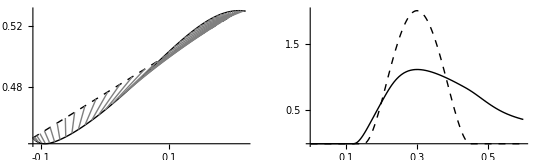

```mathematica
SetTrial[0];

(* Joint trajectories *)
elbAng=NtoD["angleElbow"]/Degree;
elbDes = NtoD["desElbow"]/Degree;
elbCom = NtoD["comElbow"]/Degree;
angleElb =TimePlotD[elbAng,{PlotStyle->{Black}, AxesLabel->{"time","angle"}}];
desAngleElb = TimePlotD[elbDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleElb = TimePlotD[elbCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];

shdAng=NtoD["angleShoulder"]/Degree;
shdDes = NtoD["desShoulder"]/Degree;
shdCom = NtoD["comShoulder"]/Degree;
angleShd= TimePlotD[shdAng,{PlotStyle->{Black}}];
desAngleShd = TimePlotD[shdDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleShd = TimePlotD[shdCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
elbow = Show[angleElb, desAngleElb, comAngleElb];
shoulder = Show[angleShd, desAngleShd, comAngleShd];

(* Calculate derivatives *)
accScale = 10;

velElb= TimePlot["velocityElbow",{PlotStyle->{Black}, AxesLabel->{"time","velocity"}}];
desVelElbD = Differences[NtoD["desElbow", bestFitDelay]]/dt;
desVelElbD = PadRight[desVelElbD,Length[time],Last[desVelElbD]];
desVelElb = TimePlotD[desVelElbD,{PlotStyle->{Black,Dashed}}];
desAccElbD = Differences[desVelElbD]/dt/accScale;
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElbD = MovingAverage[desAccElbD,3];
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElb = TimePlotD[desAccElbD,{PlotStyle->{Gray}}];

velShd= TimePlot["velocityShoulder",{PlotStyle->{Black}}];
desVelShdD = Differences[NtoD["desShoulder", bestFitDelay]]/dt;
desVelShdD = Append[desVelShdD,desVelShdD[[Length[desVelShdD]]]];
desVelShd = TimePlotD[desVelShdD,{PlotStyle->{Black,Dashed}}];
desAccShdD = Differences[desVelShdD]/dt/accScale;
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShdD = MovingAverage[desAccShdD,3];
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShd = TimePlotD[desAccShdD,{PlotStyle->{Gray}}];

velsElb = Show[velElb, desVelElb, desAccElb];
velsShd = Show[velShd, desVelShd, desAccShd];
vels = Show[velElb,velShd];

(* Forces applied at joints, total is more or less acceleration *)
itElbD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msElbD = NtoD["torqueElbow"];
totalElbD = msElbD +itElbD;
totalElb = TimePlotD[totalElbD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, AxesLabel->{"time","forceElb"}}];
trqElb= TimePlot["torqueElbow",{PlotStyle->Black}];
itElb = TimePlotD[itElbD,{PlotStyle->{Black,Dashed}}];
(*opttotalP = TimePlotOptima[totalElbD, time];
optitP = TimePlotOptima[itElbD, time];
optmsP = TimePlotOptima[msElbD, time];*)
trqsElb = Show[totalElb,trqElb, itElb(*, opttotalP,optitP, optmsP*)];

(*Maxima[totalElbD,time][[1]]*)

itShdD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
totalShdD = NtoD["torqueShoulder"]+itShdD;
totalShd = TimePlotD[totalShdD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},AxesLabel->{"time","forceShd"}}];
trqShd= TimePlot["torqueShoulder",{PlotStyle->Black}];
itShd = TimePlotD[itShdD,{PlotStyle->{Black,Dashed}}];
trqsShd = Show[totalShd,trqShd, itShd];


(* Effector space trajectories, i.e. cartesian position *)
xPos = TimePlot["x",{PlotStyle->{Black}, AxesLabel->{"time","x,y"}}];
desX = TimePlot["desX",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comX = TimePlot["comX",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
yPos = TimePlot["y",{PlotStyle->{Black}}];
desY = TimePlot["desY",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comY = TimePlot["comY",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
pos = Show[xPos,yPos, desX, desY];
posX = Show[xPos, desX, comX];
posY = Show[yPos, desY, comY];

(* XY plot *)
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->Black,AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
startPos = Graphics[{PointSize[Large],Point[First[positions]]}];
desX = Shift[NtoD["desX"],-50];
desY = Shift[NtoD["desY"],-50];
desPos = Transpose[{desX,desY}];
desCartPos = ListLinePlot[desPos,plotOptions,PlotStyle->{Black,Dashed},AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
sample=Table[{positions[[i]],desPos[[i]]},{i,50,Length[desPos],10}];
paral=Graphics[{Gray,Line[sample]}];
xyPos = Show[cartesianPos,desCartPos,paral];

(* Calculate tangential velocity *)
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]];
tangVel=TimePlotD[vels,{PlotStyle->{Black},AxesLabel->{"time","vel"}}];
desVels = Map[Norm,Differences[desPos]]/dt;
desVels = PadRight[desVels,Length[time],Last[desVels]];
tangDesVel = TimePlotD[desVels,{PlotStyle->{Black,Dashed},AxesLabel->{"time","vel"}}];
cartVels = Show[tangVel,tangDesVel]; 

(*(gg=GraphicsGrid[{{pos,angles,vels},{accs,trqsElb, trqsShd}}, ImageSize->{1200}]*)
armPlots=GraphicsGrid[{{xyPos, cartVels},{posX, posY},{elbow, shoulder}, {velsElb,velsShd}, {trqsElb,trqsShd}}, ImageSize->graphicsWidth];

posVelPl = GraphicsRow[{
Show[xyPos,Ticks->{LinTicks[-0.15,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.45,0.53,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}], 
Show[cartVels,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,2,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}]
},ImageSize->19cm]

(*Export["export.pdf", gg, "pdf"]*)
(*Export[figExpPath<>"Ablation1.eps",posVelPl]*)
```

## Reflex plots

```mathematica
(* Input: desired contraction modified by intersegmental input *)
desContrElbAgP =  TimePlot["reflexElbDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrElbAnP =  TimePlot["reflexElbDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrElbAgP =  TimePlot["reflexElbComContractionAg",{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlot["reflexElbComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrElbAgP =  TimePlot["reflexElbActContractionAg",{PlotStyle->{LightGray}}];
actContrElbAnP =  TimePlot["reflexElbActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrElbPlot =Show[desContrElbAgP,desContrElbAnP,comContrElbAgP,comContrElbAnP,actContrElbAgP,actContrElbAnP];

desContrShdAgP =  TimePlot["reflexShdDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrShdAnP =  TimePlot["reflexShdDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrShdAgP =  TimePlot["reflexShdComContractionAg",{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlot["reflexShdComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrShdAgP =  TimePlot["reflexShdActContractionAg",{PlotStyle->{LightGray}}];
actContrShdAnP =  TimePlot["reflexShdActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrShdPlot =Show[desContrShdAgP,desContrShdAnP,comContrShdAgP,comContrShdAnP,actContrShdAgP,actContrShdAnP];

(* Overall output: alpha MN *)
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ];

aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ];

(* Open loop activation *)
oplpElbAgP =  TimePlot["reflexElbOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpElbAnP =  TimePlot["reflexElbOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpElbPlot=Show[oplpElbAgP,oplpElbAnP ];

oplpShdAgP =  TimePlot["reflexShdOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpShdAnP =  TimePlot["reflexShdOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpShdPlot=Show[oplpShdAgP,oplpShdAnP ];

(* Spindles *)
spElbAgP =  TimePlot["reflexElbSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spElbAnP =  TimePlot["reflexElbSpResAn",{PlotStyle->{Black,Dashed}}];
spindleElbPlot =Show[spElbAgP,spElbAnP ];

spShdAgP =  TimePlot["reflexShdSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spShdAnP =  TimePlot["reflexShdSpResAn",{PlotStyle->{Black,Dashed}}];
spindleShdPlot =Show[spShdAgP,spShdAnP ];

(* Spindles components*)
spElbAgPosP =  TimePlot["reflexElbPosResAg",{PlotStyle->Black, AxesLabel->{"time","spCmpAg"}}];
spElbAgVelP =  TimePlot["reflexElbVelResAg",{PlotStyle->{Black,Dashed}}];
spElbAgDmpP =  TimePlot["reflexElbDmpResAg",{PlotStyle->{Black,Dotted}}];
spShdAgPosP =  TimePlot["reflexShdPosResAg",{PlotStyle->Black}];
spShdAgVelP =  TimePlot["reflexShdVelResAg",{PlotStyle->{Black,Dashed}}];
spShdAgDmpP =  TimePlot["reflexShdDmpResAg",{PlotStyle->{Black,Dotted}}];
spCmpElbAgPlot =Show[spElbAgPosP,spElbAgVelP,spElbAgDmpP];
spCmpShdAgPlot =Show[spShdAgPosP,spShdAgVelP,spShdAgDmpP];

spElbAnPosP =  TimePlot["reflexElbPosResAn",{PlotStyle->Black, AxesLabel->{"time","spCmpAn"}}];
spElbAnVelP =  TimePlot["reflexElbVelResAn",{PlotStyle->{Black,Dashed}}];spElbAnDmpP =  TimePlot["reflexElbDmpResAn",{PlotStyle->{Black,Dotted}}];
spShdAnPosP =  TimePlot["reflexShdPosResAn",{PlotStyle->Black}];
spShdAnVelP =  TimePlot["reflexShdVelResAn",{PlotStyle->{Black,Dashed}}];spShdAnDmpP =  TimePlot["reflexShdDmpResAn",{PlotStyle->{Black,Dotted}}];
spCmpElbAnPlot =Show[spElbAnPosP,spElbAnVelP,spElbAnDmpP];
spCmpShdAnPlot =Show[spShdAnPosP,spShdAnVelP,spShdAnDmpP];

(* IaIn activation *)
iainElbAgP =  TimePlot["reflexElbIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainElbAnP =  TimePlot["reflexElbIaInAn",{PlotStyle->{Black,Dashed}}];
iainElbPlot=Show[iainElbAgP,iainElbAnP ];
iainShdAgP =  TimePlot["reflexShdIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainShdAnP =  TimePlot["reflexShdIaInAn",{PlotStyle->{Black,Dashed}}];
iainShdPlot=Show[iainShdAgP,iainShdAnP ];

(* IbIn activation *)
ibinElbAgP =  TimePlot["reflexElbIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinElbAnP =  TimePlot["reflexElbIbInAn",{PlotStyle->{Black,Dashed}}];
ibinElbPlot=Show[ibinElbAgP,ibinElbAnP ];
ibinShdAgP =  TimePlot["reflexShdIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinShdAnP =  TimePlot["reflexShdIbInAn",{PlotStyle->{Black,Dashed}}];
ibinShdPlot=Show[ibinShdAgP,ibinShdAnP ];

(* Rn activation *)
rnElbAgP =  TimePlot["reflexElbRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnElbAnP =  TimePlot["reflexElbRenshawAn",{PlotStyle->{Black,Dashed}}];
rnElbPlot=Show[rnElbAgP,rnElbAnP ];
rnShdAgP =  TimePlot["reflexShdRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnShdAnP =  TimePlot["reflexShdRenshawAn",{PlotStyle->{Black,Dashed}}];
rnShdPlot=Show[rnShdAgP,rnShdAnP ];

reflexPlots = GraphicsGrid[{{desContrElbPlot, desContrShdPlot},{aMNElbPlot, aMNShdPlot}, {oplpElbPlot,oplpShdPlot},{spindleElbPlot,spindleShdPlot},{spCmpElbAgPlot,spCmpShdAgPlot},{spCmpElbAnPlot,spCmpShdAnPlot},{iainElbPlot,iainShdPlot},{ibinElbPlot,ibinShdPlot},{rnElbPlot, rnShdPlot}}, ImageSize->graphicsWidth];
```

## Muscle Plots

```mathematica
elbAgActP = TimePlot["ElbowFlexorAct",{PlotStyle->{Black},AxesLabel->{"time","Act"}}];
elbAnActP = TimePlot["ElbowExtensorAct", {PlotStyle->{Black,Dashed}}];
elbAct = Show[elbAgActP, elbAnActP];

shdAgActP = TimePlot["ShoulderFlexorAct",{PlotStyle->{Black}}];
shdAnActP = TimePlot["ShoulderExtensorAct", {PlotStyle->{Black,Dashed}}];
shdAct = Show[shdAgActP, shdAnActP];


elbAgFrcP = TimePlot["ElbowFlexorForce",{PlotStyle->{Black},AxesLabel->{"time","Force"}}];
elbAnFrcP = TimePlot["ElbowExtensorForce", {PlotStyle->{Black,Dashed}}];
elbFrcTotal = Show[elbAgFrcP, elbAnFrcP];

shdAgFrcP = TimePlot["ShoulderFlexorForce",{PlotStyle->{Black}}];
shdAnFrcP = TimePlot["ShoulderExtensorForce", {PlotStyle->{Black,Dashed}}];
shdFrcTotal = Show[shdAgFrcP, shdAnFrcP];


elbAgLengthP = TimePlot["ElbowFlexorLengthNorm",{PlotStyle->{Black},AxesLabel->{"time","Length"}}];
elbAnLengthP = TimePlot["ElbowExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
elbAgVelP = TimePlot["ElbowFlexorVelocityNorm",{PlotStyle->{Gray}}];
elbAnVelP = TimePlot["ElbowExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
elbKin = Show[elbAgLengthP,elbAnLengthP(*,elbAgVelP,elbAnVelP*)];

shdAgLengthP = TimePlot["ShoulderFlexorLengthNorm",{PlotStyle->{Black}}];
shdAnLengthP = TimePlot["ShoulderExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
shdAgVelP = TimePlot["ShoulderFlexorVelocityNorm",{PlotStyle->{Gray}}];
shdAnVelP = TimePlot["ShoulderExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
shdKin = Show[shdAgLengthP,shdAnLengthP(*,shdAgVelP,shdAnVelP*)];

elbAgActFrcP = TimePlot["ElbowFlexorFrcAct", {PlotStyle->{Black},AxesLabel->{"time","FrcCmp"}}];
elbAnActFrcP = TimePlot["ElbowExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
elbAgVelFrcP = TimePlot["ElbowFlexorFrcVel", {PlotStyle->{Gray},AxesLabel->{"time","FrcCmp"}}];
elbAnVelFrcP = TimePlot["ElbowExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
elbAgPsvFrcP = TimePlot["ElbowFlexorFrcPsv", {PlotStyle->{LightGray},AxesLabel->{"time","FrcCmp"}}];
elbAnPsvFrcP = TimePlot["ElbowExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
elbFrc = Show[elbAgActFrcP, elbAnActFrcP,elbAgVelFrcP,elbAnVelFrcP(*,elbAgPsvFrcP,elbAnPsvFrcP*)];

shdAgActFrcP = TimePlot["ShoulderFlexorFrcAct", {PlotStyle->{Black}}];
shdAnActFrcP = TimePlot["ShoulderExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
shdAgVelFrcP = TimePlot["ShoulderFlexorFrcVel", {PlotStyle->{Gray}}];
shdAnVelFrcP = TimePlot["ShoulderExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
shdAgPsvFrcP = TimePlot["ShoulderFlexorFrcPsv", {PlotStyle->{LightGray}}];
shdAnPsvFrcP = TimePlot["ShoulderExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
shdFrc = Show[shdAgActFrcP, shdAnActFrcP,shdAgVelFrcP,shdAnVelFrcP(*,shdAgPsvFrcP,shdAnPsvFrcP*)];


shdNetTrq = NtoD["ShoulderFlexorTorque", bestFitDelay] - NtoD["ShoulderExtensorTorque"];
elbNetTrq = NtoD["ElbowFlexorTorque", bestFitDelay] - NtoD["ElbowExtensorTorque"];
elbNetTrqP = TimePlotD[elbNetTrq,{}];
shdNetTrqP = TimePlotD[shdNetTrq,{}];

elbAgMaP = TimePlot["ElbowFlexorMomentArm",{PlotStyle->{Black},AxesLabel->{"time","MA"}}];
elbAnMaP = TimePlot["ElbowExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
elbAgTorqueP = TimePlot["ElbowFlexorTorque",{PlotStyle->{Black},AxesLabel->{"time","Torque"}}];
elbAnTorqueP = TimePlot["ElbowExtensorTorque", {PlotStyle->{Black,Dashed}}];
elbTrq = Show[elbAgTorqueP,elbAnTorqueP, elbNetTrqP];
elbMa = Show[elbAgMaP, elbAnMaP];

shdAgMaP = TimePlot["ShoulderFlexorMomentArm",{PlotStyle->{Black}}];
shdAnMaP = TimePlot["ShoulderExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
shdAgTorqueP = TimePlot["ShoulderFlexorTorque",{PlotStyle->{Black}}];
shdAnTorqueP = TimePlot["ShoulderExtensorTorque", {PlotStyle->{Black,Dashed}}];
shdTrq = Show[shdAgTorqueP,shdAnTorqueP, shdNetTrqP];
shdMa = Show[shdAgMaP, shdAnMaP];

musclePlots = GraphicsGrid[{{elbAct,shdAct},{elbFrcTotal,shdFrcTotal},{elbKin,shdKin},{elbFrc,shdFrc},{elbMa,shdMa},{elbTrq,shdTrq}},ImageSize->graphicsWidth];
```

## Phase Space plots

```mathematica
angleElbD = NtoD["angleElbow"];
velElbD = NtoD["velocityElbow"];
desAngleElbD = NtoD["desElbow",bestFitDelay];
actElbPhase = ListLinePlot[Transpose[{angleElbD,velElbD}],PlotStyle->Black,AxesLabel->{"angle","vel"},plotOptions];
desElbPhase = ListLinePlot[Transpose[{desAngleElbD,desVelElbD}],PlotStyle->{Black,Dashed},plotOptions];
elbPhase = Show[actElbPhase,desElbPhase];

angleShdD = NtoD["angleShoulder"];
velShdD = NtoD["velocityShoulder"];
desAngleShdD = NtoD["desShoulder",bestFitDelay];
actShdPhase = ListLinePlot[Transpose[{angleShdD,velShdD}],PlotStyle->Black,AxesLabel->{"angle","vel"}, plotOptions];
desShdPhase = ListLinePlot[Transpose[{desAngleShdD,desVelShdD}], PlotStyle->{Black,Dashed},plotOptions];
shdPhase = Show[actShdPhase, desShdPhase];

phSpacePlots =GraphicsRow[{elbPhase, shdPhase}, ImageSize->graphicsWidth];
```

## Output

Arm States

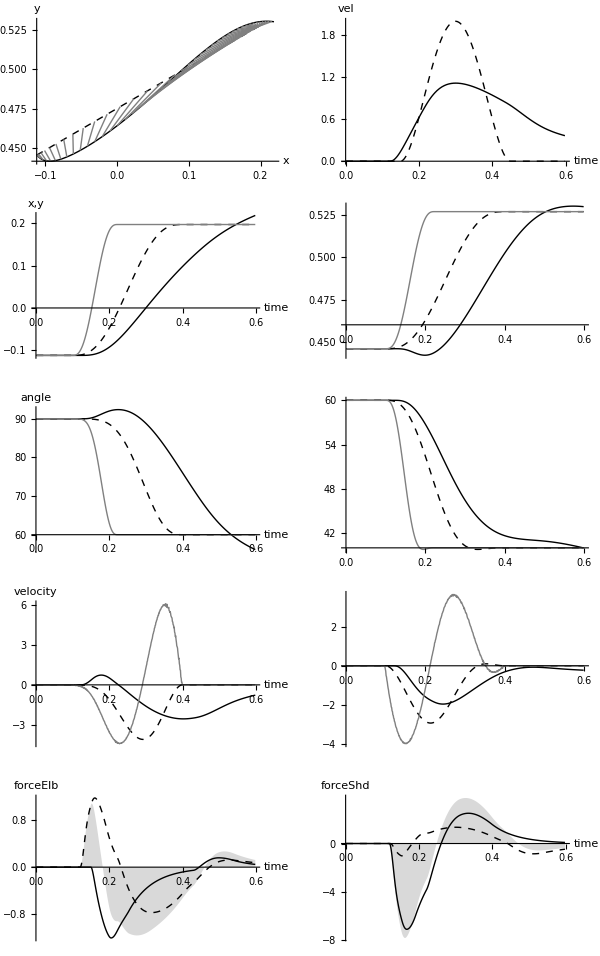

Reflex States

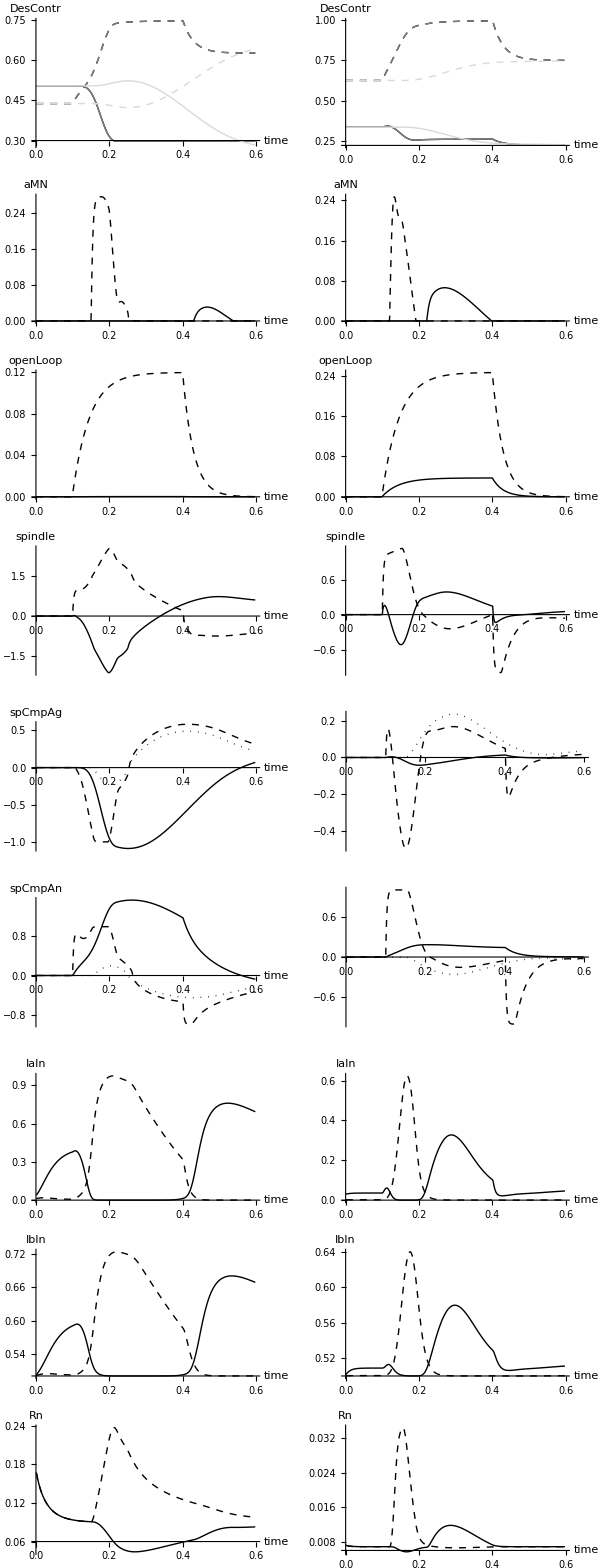

Muscle States

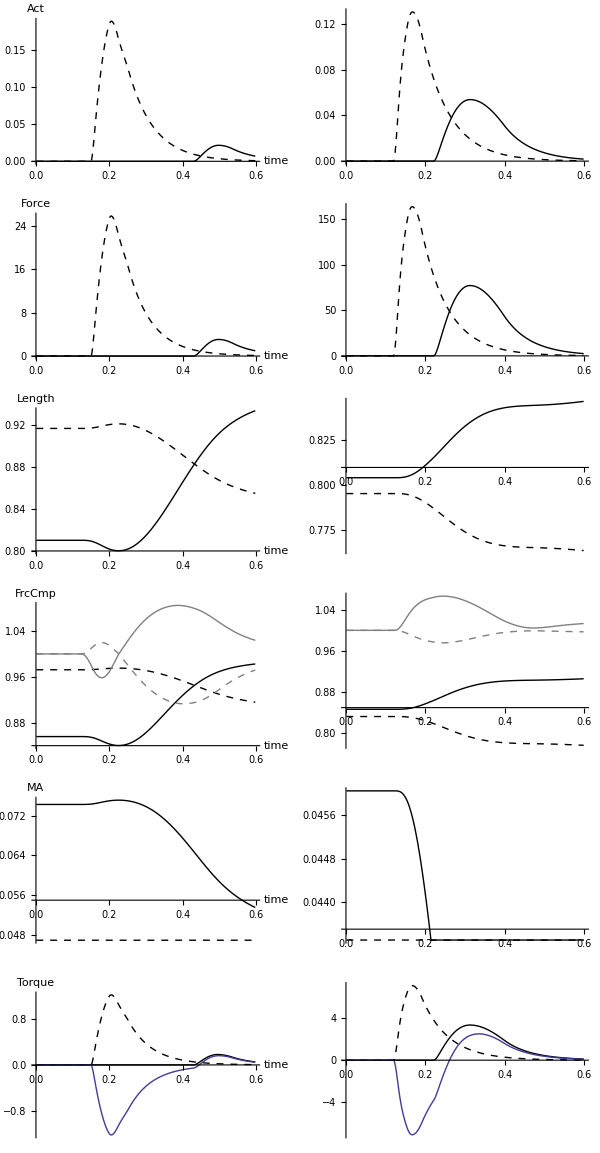

Phase space

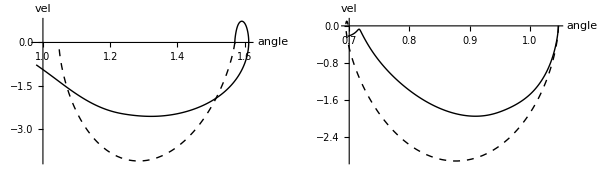

```mathematica
Print[Style["Arm States","Subtitle"]]
armPlots

Print[Style["Reflex States","Subtitle"]]
reflexPlots

Print[Style["Muscle States","Subtitle"]]
musclePlots

Print[Style["Phase space","Subtitle"]]
phSpacePlots
```

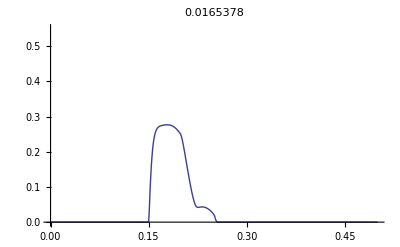

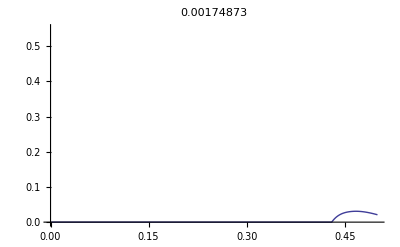

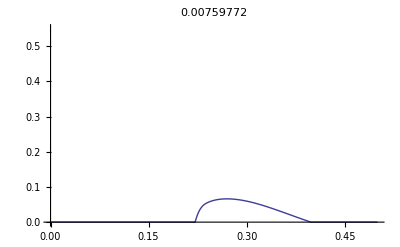

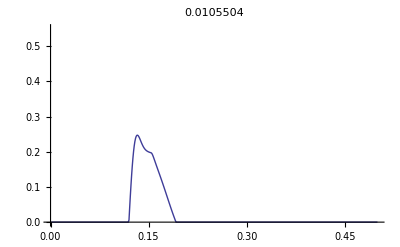

```mathematica
SetTrial[0];

ImpArea[tr_,var_,fr_,to_]:=Module[{},
SetTrial[tr];
s=NtoD[var];
s=s[[fr;;to]];
l=Length[s];
t = 0.001*Range[1,l];
d=ConstantArray[0.001,l];
ListLinePlot[Transpose[{t,s}],PlotRange->{Automatic,{0,0.55}},PlotLabel->Dot[d,s]]
];

ImpArea[0,"reflexElbMNAn",1,500]
ImpArea[0,"reflexElbMNAg",1,500]
ImpArea[0,"reflexShdMNAg",1,500]
ImpArea[0,"reflexShdMNAn",1,500]
```